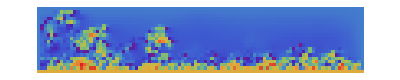

```mathematica
length=20;
width=100;
p=Table[0,{i,1,length},{j,1,width}];
Do[p[[length]][[j]]=1,{j,1,width}];
Do[
{
Do[Do[
{
p[[i]][[j]]=(p[[i+1]][[j]]+p[[i]][[j+1]]+p[[i-1]][[j]]+p[[i]][[j-1]])*0.25,
If[p[[i]][[j]]>0,p[[i]][[j]]=p[[i]][[j]]+RandomChoice[{-0.5,0,0.45}]]

}
,{j,2,width-1}]
,{i,2,length-1}],
plt[k]=ArrayPlot[p,ColorFunction->ColorData["SunsetColors"]]},
{k,1,400}]
ArrayPlot[p,ColorFunction->"Rainbow"]
gif=Table[plt[i],{i,1,400}];
Export["E:\\test_gif(6).gif",gif];
```

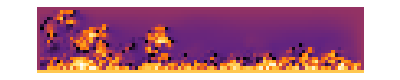

```mathematica
ArrayPlot[p,ColorFunction->ColorData["SunsetColors"]]
```